# GridMethod2D_PA

## Unofficial version, May 2015

## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
<<GridMethod2D_PA.m
```

This lists key functions defined in the package:

## Get documentation

```mathematica
?PlotGridVectors
?DualizeGrid
?PlotDualTiling
?PlotColors
?PlotColors2
?PlotSingular
```

### Runs key functions

```mathematica
kmin=-5;
kmax=5;
F1=2;
F0=1;
gamma="rand2";
groups={1,2,3,4};
```

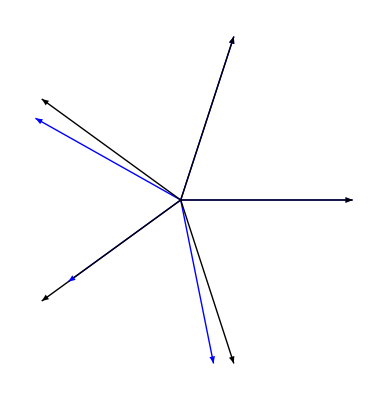

```mathematica
PlotGridVectors[F1,F0]
```

```mathematica
til=DualizeGrid[kmin,kmax,F1,F0,gamma];
```

{1.,1.,0.970043,0.809017,0.970043}

note: translation vector gamma is chosen for first two components

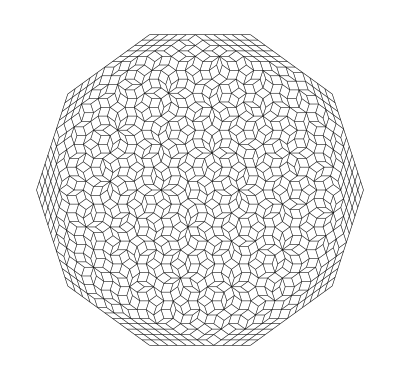

```mathematica
PlotDualTiling[til,True,False,1/1000]
```

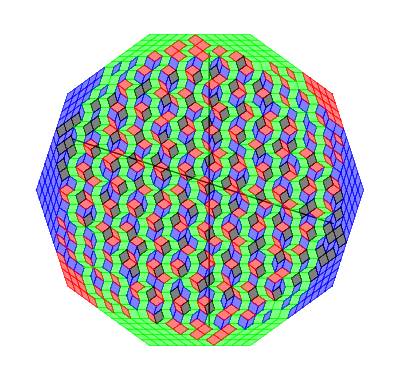

```mathematica
PlotColors[til,groups,True,True,True,1/1000,1/300,15]
```

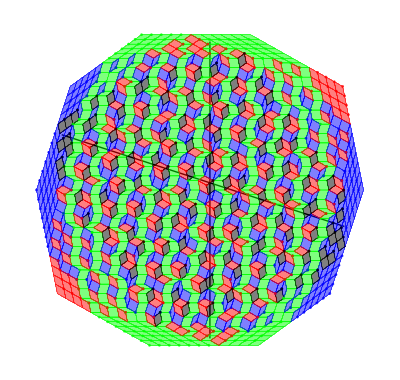

```mathematica
PlotColors2[til,F1,F0,groups,True,True,True,1/1000,1/200,15]
```

note: translation vector gamma is chosen for first two components

gamma = {0.668693,0.8312,-0.253093,-0.749946,-0.496854}

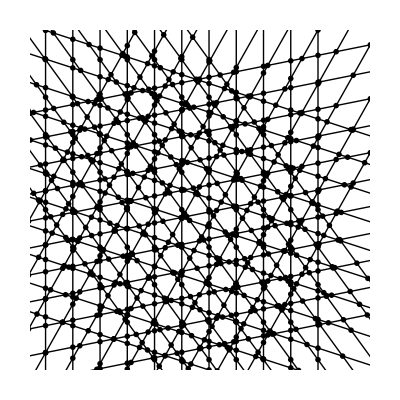

```mathematica
PlotSingular[til,kmin,kmax,F1,F0,gamma,10^-4,6]
```